# Boson-cloud metric evaluator

Notebook version of boson_cloud_metric.wl: evaluates the reconstructed metric perturbation h_ab of the boson cloud (traceful ORG, plus the ER completion), and its derivatives of any order, at any (r, χ), from the spectral data h_ORG_cloud.mx / .wdx exported by boson_cloud_pipeline_diag.wl. All functions return physical values, A^2 h with the amplitude A^2 of the run (cloud mass 10^-4 M: A^2 = 3.99×10^-9); the option "Amplitude" -> "Unit" gives them per unit A^2.

How to use: Evaluation > Evaluate Notebook (or evaluate the cells of “Definitions” in order, then “Load and self-test” and “Examples”). The definitions span several cells inside one package context: evaluate them in order, from the first. The data file is looked for in ../diag_11688456 relative to this notebook; edit dataFile if it is elsewhere. Do not give r or χ global values (the stored completion expressions use these symbols).

## Conventions and formulas

boson_cloud_metric.wl -- evaluate the reconstructed metric perturbation of the boson cloud, and its derivatives, at any (r, chi),
from the spectral data exported by boson_cloud_pipeline_diag.wl (h_ORG_cloud.mx or h_ORG_cloud.wdx).

Usage
Get["boson_cloud_metric.wl"];
loadMetric["/path/to/diag_11688456/h_ORG_cloud.wdx"];      (* or .mx (same Wolfram version / OS only) *)
bcmSelfTest[]                                               (* reference values, coframe, derivatives: run once *)

hComponent["hmbmb", r, chi]              A^2 h_{mbar mbar} (particular ORG solution)
hComponent["hlmb",  r, chi, {i, j}]      d^i/dr^i d^j/dchi^j of A^2 h_{l mbar}
hTetrad[r, chi]                          all tetrad components (ll, lm, lmb, mm, mbmb, mmb), A^2 (h_ORG + h_comp)
hTetrad[r, chi, {i, j}, "Completion" -> False, "Amplitude" -> "Unit"]
hCoord[r, chi, {i, j}]                   coordinate components h_{mu nu}, mu, nu in (v, r, chi, phi)   (4 x 4 matrix)
gKerr[r, chi, {i, j}]                    Kerr background g_{mu nu} (M = 1, a = threshold spin) in the same coordinates
gTotal[r, chi, {i, j}]                   gKerr + A^2 (h_ORG + h_comp)   (the full metric to first order in A^2)

Conventions (as in the pipeline): M = 1; ingoing Kerr coordinates (v, r, chi = cos theta, phi); boosted Kinnersley tetrad
l, n = -d_r, m, mbar; traceful ORG h_{ab} n^b = 0; delta G_ab[h] = T_ab (8 pi G = 1). Everything (T_ab, h_ORG, the completion) is per unit
amplitude^2 A^2 of the Leaver normalization; the physical perturbation is A^2 (h_ORG + h_comp) with A^2 = completion["amp2"]
(A^2 = 3.99e-9 for a cloud of mass 1e-4 M in diag_11688456). All functions return PHYSICAL values (times A^2) by default;
the option "Amplitude" -> "Unit" (hComponent, hCompletion, hTetrad, hCoord) gives them per unit A^2.
Tetrad components (order l, n, m, mbar):  ll, lm, lmb (= l mbar), mm, mbmb (= mbar mbar), mmb (= m mbar); all n-components vanish.
h_lm = conj(h_lmb), h_mm = conj(h_mbmb) (real metric); h_ll, h_mmb are real.

How each component is rebuilt (same formulas as the pipeline, sections 10, 11, 15):
h_mbmb = sum_l Y_l(chi) [ -4 (r + i a chi)/(r - i a chi)^2 I3_l(r) - 2 (r + i a chi)^2/(r - i a chi)^2 I2_l(r) ],  Y_l = _{-2}Y_{l0};
I2, I3 from their per-panel Chebyshev coefficients for r - r+ < xMax, closed-form (Legendre Q) tails beyond.
h_mmb  = -(1 - chi^2) P(chi)^2 [ K2(r) + 2 r/(r^2 + a^2 chi^2) K3(r) ]  (S = sqrt(1 - chi^2) P); zero beyond xMax (|h| < e^{2 q xMax}).
h_lmb, h_ll: 2D Chebyshev interpolation of the node values (radial panel x chi); h_lmb is interpolated as h_lmb/sin(theta).
Outer region r > rMax: panels in zeta = rMax/r.
Derivatives are exact derivatives of these representations (Chebyshev differentiation, symbolic chain/Leibniz rules), to any order.
Inputs are converted to the working precision of the run (wp = 60 digits): give r, chi as exact numbers or with >= wp digits;
machine numbers are used as exact decimals (SetPrecision). Valid for r >= r+ and -1 <= chi <= 1 (chi-derivatives of h_lmb, which contains
sin(theta), are singular at chi = +-1).

## Definitions

```mathematica
BeginPackage["BosonCloudMetric`"];
loadMetric::usage="loadMetric[file] loads h_ORG_cloud.mx or h_ORG_cloud.wdx exported by boson_cloud_pipeline_diag.wl.";
hComponent::usage="hComponent[comp, r, chi, {i, j}] gives d^i/dr^i d^j/dchi^j of the ORG tetrad component comp (\"hmbmb\", \"hmmb\", \"hlmb\", \"hll\") of the particular solution. {i, j} defaults to {0, 0}. Option \"Amplitude\" -> \"Physical\" (default: times A^2 of the run) or \"Unit\" (per unit A^2).";
hCompletion::usage="hCompletion[r, chi, {i, j}] gives the completion (ER zero modes with the Komar-fixed amplitudes) as an Association of tetrad components ll, lm, lmb. Option \"Amplitude\" -> \"Physical\" (default) or \"Unit\".";
hTetrad::usage="hTetrad[r, chi, {i, j}, opts] gives all tetrad components (ll, lm, lmb, mm, mbmb, mmb) of h_ORG + h_comp (options \"Completion\" -> True|False, \"Amplitude\" -> \"Physical\" (default) | \"Unit\").";
hCoord::usage="hCoord[r, chi, {i, j}, opts] gives the coordinate components h_{mu nu} (mu, nu = v, r, chi, phi) as a 4 x 4 matrix; same options as hTetrad.";
gKerr::usage="gKerr[r, chi, {i, j}] gives the (i, j) derivative of the Kerr metric g_{mu nu} (M = 1, a = threshold spin) in ingoing coordinates (v, r, chi, phi).";
gTotal::usage="gTotal[r, chi, {i, j}, opts] gives gKerr + A^2 (h_ORG + h_comp) (option \"Completion\" -> True|False).";
bcmParameters::usage="bcmParameters[] gives the run parameters, grid sizes and completion data.";
bcmSelfTest::usage="bcmSelfTest[] checks the rebuilt components against the reference values of the run, the coframe against the stored completion, and the derivatives against finite differences.";
Begin["`Private`"];
```

### loading

```mathematica
loadMetric[file_String]:=Module[{d},If[!FileExistsQ[file],Message[loadMetric::nofile,file];Return[$Failed]];If[ValueQ[r]||ValueQ[χ],Message[loadMetric::glob];Return[$Failed]];d=Block[{$Context="Global`",$ContextPath={"System`","Global`"}},Import[file]];If[!AssociationQ[d],Message[loadMetric::bad,file];Return[$Failed]];setup[d];Print["loaded ",file,":  a = ",N[aN,15],",  lmax = ",Max[lList],",  wp = ",wp,",  ",nPan," inner + ",nOut," outer panels x ",nPn," nodes,  nchi = ",nchi,",  A^2 = ",N[amp2,12]];];
loadMetric::nofile="file `1` not found.";
loadMetric::bad="`1` does not contain the expected Association.";
loadMetric::bcmnl="no data loaded: call loadMetric[file] first.";
loadMetric::glob="Global`r or Global`χ has a value; the exported expressions use these symbols. Clear them (Clear[r, χ]) and load again.";
rcSub[e_,rv_,cv_]:=e/.s_Symbol/;Context[s]=!="System`"&&MemberQ[{"r","χ"},SymbolName[s]]:>If[SymbolName[s]==="r",rv,cv];
setup[d_]:=Module[{g=d["grid"],p=d["params"]},dat=d;wp=p["wp"];aN=p["a"];rp=p["rplus"];kap=√(1-aN^2);xB=g["xB"];xMax=g["xMax"];nPn=g["nPn"];nchi=g["nchi"];zB=g["zetaB"];nPan=Length[xB]-1;nOut=Length[zB]-1;rMax=rp+xMax;chiN=g["chiNodes"];sN=√(1-chiN^2);lList=d["hmbmb"]["lList"];I123=d["hmbmb"]["I123"];gC=d["hmbmb"]["g"];Cup=d["hmbmb"]["Cup"];K123=d["hmmb"]["K123"];tauC=d["hmmb"]["tau"];Ppoly=Evaluate[rcSub[d["hmmb"]["PpolyR"],0,#1]]&;nodes["hlmb"]={d["hlmb"]["inner"],d["hlmb"]["outer"]};nodes["hll"]={d["hll"]["inner"],d["hll"]["outer"]};comp=d["completion"];amp2=comp["amp2"];{cM,cA}=comp["coefficients"];cache=Association[];loaded=True;];
loaded=False;cache=Association[];
SetAttributes[memo,HoldRest];
memo[key_,expr_]:=If[KeyExistsQ[cache,key],cache[key],cache[key]=expr];
check[]:=If[TrueQ[loaded],True,Message[loadMetric::bcmnl];Abort[]];
```

### numbers and Chebyshev utilities (as in the pipeline)

```mathematica
toWP[x_]:=Which[Precision[x]===∞,N[x,wp],Precision[x]===MachinePrecision,SetPrecision[x,wp],True,x];
chebMat[nn_]:=memo[{"chebMat",nn},N[Table[(2 If[k==0,1/2,1] Cos[(k π (j+1/2))/nn])/nn,{k,0,nn-1},{j,0,nn-1}],wp]];
chebDer[c_List]:=Module[{nn=Length[c]-1,dd},dd=ConstantArray[0,nn+2];Do[dd⟦k⟧=dd⟦k+2⟧+2 k c⟦k+1⟧,{k,nn,1,-1}];dd⟦1⟧=dd⟦1⟧/2;Take[dd,nn+1]];
chebEval[c_List,z_]:=c.ChebyshevT[Range[0,Length[c]-1],z];
panelIndex[x_]:=Min[nPan,Max[1,LengthWhile[xB,#1≤x&]]];
panMid[p_]:=1/2 (xB⟦p⟧+xB⟦p+1⟧);panH[p_]:=1/2 (xB⟦p+1⟧-xB⟦p⟧);
zMid[q_]:=1/2 (zB⟦q⟧+zB⟦q+1⟧);zH[q_]:=1/2 (zB⟦q+1⟧-zB⟦q⟧);
panelEval[coefs_,r0_,d_]:=Module[{x=r0-rp,p,t},p=panelIndex[x];t=(x-panMid[p])/panH[p];chebEval[Nest[chebDer,coefs⟦p⟧,d],t]/panH[p]^d];
```

```mathematica
Pder[l_,k_,c_]:=If[k>l,0,(2 k-1)!! GegenbauerC[l-k,k+1/2,c]];
Nl[l_]:=√(((2 l+1) (l-2)!)/(4 π (l+2)!));
Yd[l_,m_,c_]:=N[Nl[l],wp] ((1-c^2) Pder[l,m+2,c]-2 m c Pder[l,m+1,c]-m (m-1) Pder[l,m,c]);
```

### h_mbarmbar

```mathematica
QH[l_,X_]:=(√π Gamma[l+1] Hypergeometric2F1[(l+1)/2,(l+2)/2,l+3/2,1/X^2])/(Gamma[l+3/2] (2 X)^(l+1));
NUp[l_]:=((2 l+1)!!)/((l+2)! kap^(l+3));
tailF[l_,k_,d_]:=memo[{"tail",l,k,d},Module[{X,F},F=Switch[k,0,D[QH[l,X], {X,2}],1,-kap D[QH[l,X], X],2,kap^2 QH[l,X],3,(kap^3 (QH[l-1,X]-QH[l+1,X]))/(2 l+1)];Function[Evaluate[{X}],Evaluate[Cup[l] NUp[l] kap^-d D[F, {X,d}]]]]];
Ival[l_,k_,d_,r0_]:=If[r0-rp≥xMax,tailF[l,k,d][(r0-1)/kap],panelEval[If[k==0,gC[l],I123[l]⟦All,k⟧],r0,d]];
hmbD[i_,j_]:=memo[{"hmb",i,j},Module[{rr,cc,I2f,I3f,Yf,e},e=Yf[cc] (-(4 (rr+ⅈ aN cc) I3f[rr])/(rr-ⅈ aN cc)^2-(2 (rr+ⅈ aN cc)^2 I2f[rr])/(rr-ⅈ aN cc)^2);e=D[e, {rr,i},{cc,j}]/.{Derivative[n_][I3f][rr]:>i3[n],I3f[rr]:>i3[0],Derivative[n_][I2f][rr]:>i2[n],I2f[rr]:>i2[0],Derivative[m_][Yf][cc]:>y[m],Yf[cc]:>y[0]};Function[Evaluate[{rr,cc}],Evaluate[e]]]];
hmbmb[r0_,c0_,{i_,j_}]:=Module[{e=hmbD[i,j][r0,c0]},∑_l^lList (e/.{i3[n_]:>Ival[l,3,n,r0],i2[n_]:>Ival[l,2,n,r0],y[m_]:>Yd[l,m,c0]})];
```

### h_mmbar

```mathematica
hmmD[i_,j_]:=memo[{"hmm",i,j},Module[{rr,cc,K2f,K3f,e},e=-(1-cc^2) Ppoly[cc]^2 (K2f[rr]+(2 rr K3f[rr])/(rr^2+aN^2 cc^2));e=D[e, {rr,i},{cc,j}]/.{Derivative[n_][K3f][rr]:>k3[n],K3f[rr]:>k3[0],Derivative[n_][K2f][rr]:>k2[n],K2f[rr]:>k2[0]};Function[Evaluate[{rr,cc}],Evaluate[e]]]];
hmmb[r0_,c0_,{i_,j_}]:=If[r0-rp≥xMax,0 r0,hmmD[i,j][r0,c0]/.{k2[n_]:>panelEval[K123⟦All,2⟧,r0,n],k3[n_]:>panelEval[K123⟦All,3⟧,r0,n]}];
```

### h_lmbar, h_ll: 2D Chebyshev interpolation of the node values

```mathematica
c2Cache[cname_,reg_,p_,i_,j_]:=memo[{"c2",cname,reg,p,i,j},Which[i>0,Transpose[chebDer/@Transpose[c2Cache[cname,reg,p,i-1,j]]],j>0,chebDer/@c2Cache[cname,reg,p,i,j-1],True,Module[{V=nodes[cname]⟦If[reg==="in",1,2],p⟧},If[cname==="hlmb",V=(#1/sN&)/@V];chebMat[nPn].V.Transpose[chebMat[nchi]]]]];
chainOuter[n_]:=chainOuter[n]=Module[{rr,zm,zh,rM,F,e},e=D[F[(rM/rr-zm)/zh], {rr,n}]/.{Derivative[k_][F][_]:>fd[k],F[_]:>fd[0]};Function[Evaluate[{rr,zm,zh,rM}],Evaluate[Table[Coefficient[e,fd[k]],{k,0,n}]]]];
sinD[k_,c_]:=D[√(1-cc^2), {cc,k}]/.cc->c;
interpQ[cname_,r0_,c0_,i_,jq_]:=Module[{x=r0-rp,p,q,t,z0,co,Tt,Tc},Tc=ChebyshevT[Range[0,nchi-1],c0];If[x<xMax,p=panelIndex[x];t=(x-panMid[p])/panH[p];Tt=ChebyshevT[Range[0,nPn-1],t];(Tt.c2Cache[cname,"in",p,i,jq].Tc)/panH[p]^i,z0=rMax/r0;q=Min[nOut,Max[1,LengthWhile[zB,#1≤z0&]]];t=(z0-zMid[q])/zH[q];Tt=ChebyshevT[Range[0,nPn-1],t];co=chainOuter[i][r0,zMid[q],zH[q],rMax];∑_(k=0)^i co⟦k+1⟧ Tt.c2Cache[cname,"out",q,k,jq].Tc]];
hInterp[cname_,r0_,c0_,{i_,j_}]:=If[cname==="hlmb",∑_(m=0)^j Binomial[j,m] sinD[j-m,c0] interpQ[cname,r0,c0,i,m],interpQ[cname,r0,c0,i,j]];
```

### public: ORG components

```mathematica
ampF[a_]:=Switch[a,"Physical",amp2,"Unit",1,_,Message[hComponent::amp,a];Abort[]];
hComponent::amp="\"Amplitude\" must be \"Physical\" or \"Unit\", not `1`.";
Options[hComponent]={"Amplitude"->"Physical"};
hComponent[cname_String,r0_?NumericQ,c0_?NumericQ,ij:{_Integer?NonNegative,_Integer?NonNegative}:{0,0},OptionsPattern[]]:=(check[];ampF[OptionValue["Amplitude"]] hComp0[cname,r0,c0,ij]);
hComp0[cname_String,r0_?NumericQ,c0_?NumericQ,{i_Integer?NonNegative,j_Integer?NonNegative}]:=(check[];With[{rr=toWP[r0],cc=toWP[c0]},Switch[cname,"hmbmb",hmbmb[rr,cc,{i,j}],"hmmb",hmmb[rr,cc,{i,j}],"hlmb"|"hll",hInterp[cname,rr,cc,{i,j}],"hmm",Conjugate[hmbmb[rr,cc,{i,j}]],"hlm",Conjugate[hInterp["hlmb",rr,cc,{i,j}]],_,Message[hComponent::comp,cname];$Failed]]);
hComponent::comp="unknown component `1`; use \"hmbmb\", \"hmmb\", \"hlmb\", \"hll\" (or \"hmm\", \"hlm\").";
```

### completion (closed form)

```mathematica
compD[which_,i_,j_]:=memo[{"comp",which,i,j},Module[{rr,cc,e},e=rcSub[comp[which],rr,cc];Function[Evaluate[{rr,cc}],Evaluate[D[e, {rr,i},{cc,j}]]]]];
Options[hCompletion]={"Amplitude"->"Physical"};
hCompletion[r0_?NumericQ,c0_?NumericQ,ij:{_Integer?NonNegative,_Integer?NonNegative}:{0,0},OptionsPattern[]]:=(check[];(ampF[OptionValue["Amplitude"]] #1&)/@hCompletion0[r0,c0,ij]);
hCompletion0[r0_?NumericQ,c0_?NumericQ,{i_Integer?NonNegative,j_Integer?NonNegative}]:=(check[];With[{rr=toWP[r0],cc=toWP[c0]},AssociationThread[{"ll","lm","lmb"},cM compD["tetrad_ER_unit_dM",i,j][rr,cc]+cA compD["tetrad_ER_unit_da",i,j][rr,cc]]]);
```

### all tetrad components

```mathematica
Options[hTetrad]={"Completion"->True,"Amplitude"->"Physical"};
hTetrad[r0_?NumericQ,c0_?NumericQ,ij:{_Integer?NonNegative,_Integer?NonNegative}:{0,0},OptionsPattern[]]:=Module[{lmb,mbmb,h,hc,s},check[];lmb=hComp0["hlmb",r0,c0,ij];mbmb=hComp0["hmbmb",r0,c0,ij];h=Association["ll"->hComp0["hll",r0,c0,ij],"lm"->Conjugate[lmb],"lmb"->lmb,"mm"->Conjugate[mbmb],"mbmb"->mbmb,"mmb"->hComp0["hmmb",r0,c0,ij]];If[TrueQ[OptionValue["Completion"]],hc=hCompletion0[r0,c0,ij];h=Association["ll"->h["ll"]+hc["ll"],"lm"->h["lm"]+hc["lm"],"lmb"->h["lmb"]+hc["lmb"],"mm"->h["mm"],"mbmb"->h["mbmb"],"mmb"->h["mmb"]]];s=ampF[OptionValue["Amplitude"]];(s #1&)/@h];
```

### background: Kerr metric and the coframe (pipeline section 1, M = 1)

```mathematica
bgSym:=memo[{"bg"},Module[{rr,cc,a=aN,gdd,lu,nu,mu,mbu,eDu,eDd,eta},gdd={{-(1-(2 rr)/(rr^2+a^2 cc^2)),1,0,-(2 a rr (1-cc^2))/(rr^2+a^2 cc^2)},{1,0,0,-a (1-cc^2)},{0,0,(rr^2+a^2 cc^2)/(1-cc^2),0},{-(2 a rr (1-cc^2))/(rr^2+a^2 cc^2),-a (1-cc^2),0,(1-cc^2) (rr^2+a^2+(2 a^2 rr (1-cc^2))/(rr^2+a^2 cc^2))}};lu={(rr^2+a^2)/(rr^2+a^2 cc^2),(rr^2-2 rr+a^2)/(2 (rr^2+a^2 cc^2)),0,a/(rr^2+a^2 cc^2)};nu={0,-1,0,0};mu={ⅈ a √(1-cc^2),0,-√(1-cc^2),ⅈ/(√(1-cc^2))}/(√2 (rr+ⅈ a cc));mbu={-ⅈ a √(1-cc^2),0,-√(1-cc^2),-ⅈ/(√(1-cc^2))}/(√2 (rr-ⅈ a cc));eDu={lu,nu,mu,mbu};eDd=eDu.gdd;eta={{0,-1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,1,0}};{rr,cc,gdd,eta.eDd}]];
frameD[i_,j_]:=memo[{"frame",i,j},With[{b=bgSym},Function[Evaluate[{b⟦1⟧,b⟦2⟧}],Evaluate[D[b⟦4⟧, {b⟦1⟧,i},{b⟦2⟧,j}]]]]];
kerrD[i_,j_]:=memo[{"kerr",i,j},With[{b=bgSym},Function[Evaluate[{b⟦1⟧,b⟦2⟧}],Evaluate[D[b⟦3⟧, {b⟦1⟧,i},{b⟦2⟧,j}]]]]];
gKerr[r0_?NumericQ,c0_?NumericQ,{i_Integer?NonNegative,j_Integer?NonNegative}]:=(check[];kerrD[i,j][toWP[r0],toWP[c0]]);
gKerr[r0_?NumericQ,c0_?NumericQ]:=gKerr[r0,c0,{0,0}];
hTetMat[h_]:={{h["ll"],0,h["lm"],h["lmb"]},{0,0,0,0},{h["lm"],0,h["mm"],h["mmb"]},{h["lmb"],0,h["mmb"],h["mbmb"]}};
Options[hCoord]=Options[hTetrad];
hCoord[r0_?NumericQ,c0_?NumericQ,{i_Integer?NonNegative,j_Integer?NonNegative},opts:OptionsPattern[]]:=Module[{rr=toWP[r0],cc=toWP[c0],H,W},check[];H[a1_,b1_]:=H[a1,b1]=hTetMat[hTetrad[rr,cc,{a1,b1},opts]];W[a1_,b1_]:=W[a1,b1]=frameD[a1,b1][rr,cc];∑_(i1=0)^i ∑_(i2=0)^(i-i1) ∑_(j1=0)^j ∑_(j2=0)^(j-j1) Multinomial[i1,i2,i-i1-i2] Multinomial[j1,j2,j-j1-j2] Transpose[W[i1,j1]].H[i2,j2].W[i-i1-i2,j-j1-j2]];
hCoord[r0_?NumericQ,c0_?NumericQ,opts:OptionsPattern[]]:=hCoord[r0,c0,{0,0},opts];
Options[gTotal]={"Completion"->True};
gTotal[r0_?NumericQ,c0_?NumericQ,ij:{_Integer?NonNegative,_Integer?NonNegative}:{0,0},OptionsPattern[]]:=gKerr[r0,c0,ij]+hCoord[r0,c0,ij,"Completion"->OptionValue["Completion"],"Amplitude"->"Physical"];
bcmParameters[]:=(check[];Association["params"->dat["params"],"rplus"->rp,"xMax"->xMax,"rMax"->rMax,"innerPanels"->nPan,"outerPanels"->nOut,"nodesPerPanel"->nPn,"nchi"->nchi,"lList"->lList,"amp2"->amp2,"completionCoefficients"->{cM,cA},"totalMass"->comp["totalMass"],"totalAngularMomentum"->comp["totalAngularMomentum"],"conventions"->dat["conventions"]]);
```

## Load

```mathematica
dataFile = FileNameJoin[{NotebookDirectory[], "h_ORG_cloud.wdx"}];
loadMetric[dataFile];
```

loaded /Users/kelvinlam/UIUC/Research/Boson_Cloud_Reconstruction/Einstein_Code/Tools/h_ORG_cloud.wdx:  a = 0.877153027594927,  lmax = 36,  wp = 60,  245 inner + 4 outer panels x 32 nodes,  nchi = 80,  A^2 = 3.99342375869×10^-9

```mathematica
bcmParameters[]
```

<|params→<|a→0.877153027594927442291329984673486707691943001859830521417619,mu→0.3,omegac→0.29629324847975068673706070723492066435986408538107471055198,q→-0.0470139437328620344143868048857472849295437626173710095384,alpha→1.82029779666299035526702123975212236466905741118451993581,gamma→0.0412384230844574981569776712345935929026217934264026878784 ⅈ,rplus→1.4802109600801011048740217503388846593536739245153205862665,rminus→0.51978903991989889512597824966111534064632607548467941373347,wp→60,lmax→36,nChi→64,nP→32,nPn→32,nchiRec→80,omegaLeaver→0.296293248479750686737060707234920664359864085381074710551979482746208663016699268590552925291213364270002680263149738620152988853607500737650023058052934514274,Alm→2.000340108287424943505394520699475696303152976038395833307385635329137218339177254056723515361105077956451879558865285417427180308072958480528878413256680024142|>,rplus→1.4802109600801011048740217503388846593536739245153205862665,xMax→2388.,rMax→2389.4802109600801011048740217503388846593536739245153205863,innerPanels→245,outerPanels→4,nodesPerPanel→32,nchi→80,lList→{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36},amp2→3.9934237586896374612187553914981375318251365148193516×10^-9,completionCoefficients→{25041.1691928264106981630983580750564066,62549.8780053623394681290176513353774108},totalMass→1.0001,totalAngularMomentum→0.877490531066616687392456766126079144785956402235005853567,conventions→traceful ORG (h_nb = 0), boosted Kinnersley tetrad of section 1 (n = -∂_r), ingoing coordinates (v, r, χ = cosθ, ϕ~), M = 1, 8πG = 1, δG_ab[h] = T_ab; particular solution (h -> 0 at infinity); its completion (zero modes of the ER paper Eq. (B1), amplitudes fixed by the Komar/ADM charges E_cloud, J_cloud) is in the key completion|>

## Examples

Tetrad components of the ORG particular solution and derivatives d^i/dr^i d^j/dχ^j with {i, j} (shown to 15 digits; the functions return the full 60-digit values).

```mathematica
N[hComponent["hmbmb", 3, 1/2], 15]
N[hComponent["hlmb", 3, 1/2, {1, 2}], 15]
N[hComponent["hll", 5000, 21/100, {2, 0}], 15]
```

-0.0000221196670944098-9.3563442160096×10^-6 ⅈ

0.0000901817652797622-0.000012760436615606 ⅈ

1.90848058287118×10^-19+0. ⅈ

Coordinate components A^2 h_μν (μ, ν = v, r, χ, φ), the Kerr background, and the full metric g + A^2 (h_ORG + h_comp):

```mathematica
MatrixForm[N[hCoord[3, 1/2], 12]]
```

(0.0000233638083145+0. ⅈ | 0.+0. ⅈ | 0.0000206748482907+0. ⅈ | -0.0000198844584597+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000206748482907+0. ⅈ | 0.+0. ⅈ | -0.00117183458089+0. ⅈ | -0.0000378016665828+0. ⅈ
-0.0000198844584597+0. ⅈ | 0.+0. ⅈ | -0.0000378016665828+0. ⅈ | -0.00031394120724+0. ⅈ)

Radial profiles of |h| at χ = 0.87 (r - r+ from 10^-4 to 10^4):

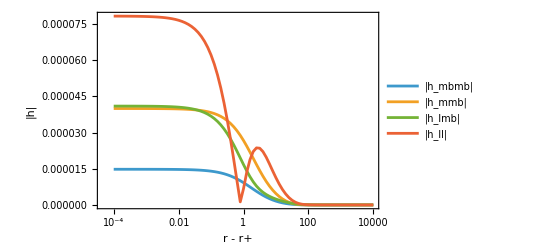

```mathematica
With[{rp = bcmParameters[]["rplus"]},
 ListLogLinearPlot[Table[Table[{x, Abs[hComponent[c, rp + x, 87/100]]}, {x, 10^Range[-4, 4, 1/10]}], {c, {"hmbmb", "hmmb", "hlmb", "hll"}}],
  Joined -> True, PlotLegends -> {"|h_mbmb|", "|h_mmb|", "|h_lmb|", "|h_ll|"}, Frame -> True, FrameLabel -> {"r - r+", "|h|"}, PlotRange -> All]]
```